## Wuschel-Ablated-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

This is a Cellzilla2D example that is based on the "Activator" model in 
H Jonsson, M Heisler, GV Reddy, V Agrawal, V Gor, BE Shapiro, E Mjolsness & EM Meyerowitz (2005) "Modeling the organization of the WUSCHEL expression domain in the shoot apical meristem," Bioinformatics, Vol. 21 Suppl. 1, 2005, pages i232-i240.

For more details on the model see
http://bioinformatics.oxfordjournals.org/cgi/content/abstract/21/suppl_1/i232

This CPU times shown reflect a core-i7 920 CPU

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.0 (8-Jan-2013)) loaded Wed 23 Jan 2013 19:21:59
using xCellerator 0.92 and XSSA 1204002
GPL License Terms Apply

```mathematica
<<xlr8r.m
```

xCellerator 0.92 (11-Nov-2012) loaded Wed 23 Jan 2013 19:22:00
using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4)
using MathSBML version 2.12

Define a cellular template to run the model on.

225 cells

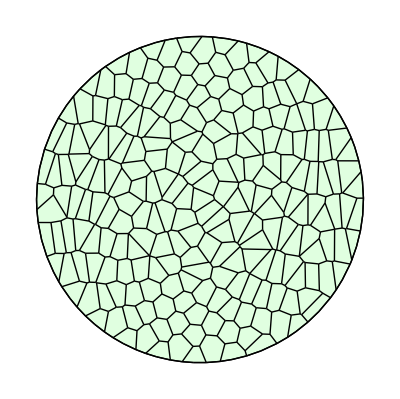

```mathematica
w=TemplateRandomCircularGrid[225,100];
Print[n=NTissueCells[w]," cells"];
ShowTissue[w]
```

Identify which cells to ablate

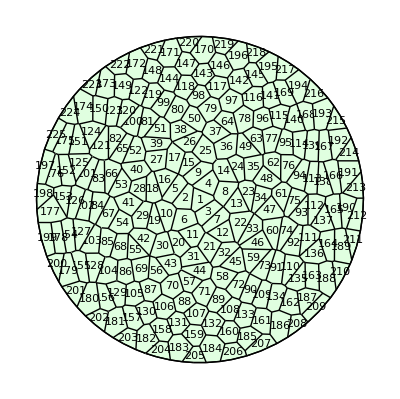

```mathematica
ShowTissue[w, "CellNumbers"-> True]
```

Punch a big hole in the center

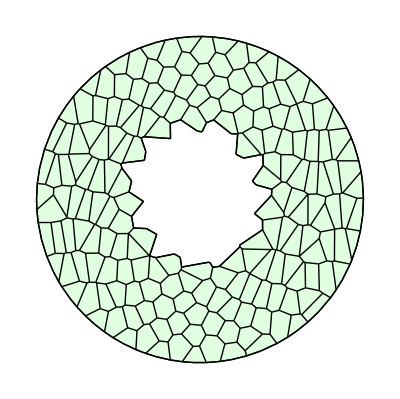

```mathematica
w1=RemoveCell[w, Range[40]];
ShowTissue[w1]
```

Identify the "L1" layer - the cells on the outer boundary - make sure to exclude the boundary of the ablated region.

```mathematica
L1Layer=Select[CellsOnBoundary[w1], #>50&]
```

{130,131,132,133,134,137,139,140,141,142,143,144,146,148,149,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185}

Define the Cellerator network that will produce the ODES as specified in the model

```mathematica
net={
{Y↦W,GRN[1/tauw,Twy,1,hw,sigma]},
{A↦W,GRN[1/tauw,Twa,1,hw,sigma]},
{W->∅,dw},{L1->Y+L1,ky},
{Y->∅,dy},
{∅⇄A,a,beta},
{A+Y->Y,d},
{2 A+B->3 A,c},
{A->B,b}};
```

Define the initial conditions of all variables. 
Here we use zero for A,B, W, Y but that is not necessary.
L1 is an indicator function that must be 1 on the boundary and zero elsewhere.

```mathematica
n=NTissueCells[w1]
```

185

```mathematica
ic[i_]:={A[i]->0,B[i]->0,W[i]->0,Y[i]->0,L1[i]->If[MemberQ[L1Layer,i],1,0]};
myic=Flatten[ic/@Range[n]];
```

Determine the large set of all Cellerator reactions in all cells, allowing A, B, and Y to diffuse with membrane penetrabilities DA, DB, and DY

```mathematica
cpu=TimeUsed[]; 
bignet=CelleratorNetwork[w1, "Reactions"-> net,"Diffusion"-> {{A,DA},{B,DB},{Y,DY}}];
cpu=TimeUsed[]-cpu;
Print[cpu, " Seconds to generate network."];
```

185 Cells.

10 internal reactions in each cell.

1850 intracellular reactions.

2868 diffusion reactions.

4718 total reactions.

0.532033 Seconds to generate network.

Define the parameters for the model

```mathematica
parameters={d-> .5,DY-> 2,  Twy->-20,Twa->0.5,ky->0.2,kz->0.2,dy->0.1,dz->0.1,DZ->0.1,kD->3.0,tauw->10,dw->0.1,hw->0,a->0.1,b->0.2,beta->0.1,c->0.1,DA->1.5,DB->15.0};
```

Run a simulation using xlr8r

```mathematica
CPU=TimeUsed[];
sim=RunSim[bignet,parameters,myic,{0,2000}, MaxSteps-> 100000];
Print[TimeUsed[]-CPU," seconds to run the simulation"];
```

4.8563 seconds to run the simulation

Plot the results of a single variable (depending upon geometry and parameter values it can go to either a steady state or it might oscillate)

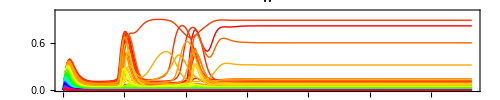

```mathematica
SimPlot[sim,W,{0,1000},PlotRange->{0,1},AspectRatio->.2,ImageSize->500,"Points"->300]
```

Use SimShowFinal to find the solution at the stop time of the simulation and automatically set the scales.

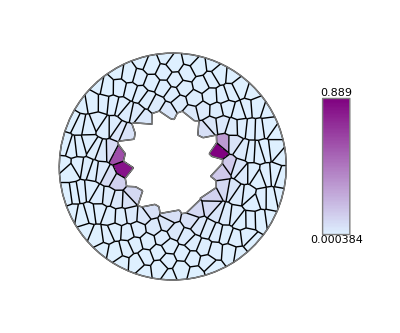

```mathematica
finalpic=SimShowFinal[sim,W,w1,{LightBlue,Purple}]
```

SimAnimate will produce a sequence of plots over time. If the start and stop time are the same only one plot will be returned.

This will generate a movie of the approach towards a steady state but it can only be viewed in Mathematica

```mathematica
m=SimAnimate[sim, W, w1, {0,500, 50}, {LightGreen, Purple}, {0, 1}];
ListAnimate[m]
```

SaveFrames, ToMOV, ToAVI create higher resolution movie files.

If ffmpeg is not installed then only the JPG files will be saved and the movie will not actually be produced.

```mathematica
m=SimAnimate[sim, W, w1, {0,500, 2}, {LightGreen, Purple}, {0, 1}];
```

```mathematica
SaveFrames[m, "JPG", 800, ".AVI", "Ablated-Activator-Model"]
```